### Graphical Interpretation of the Differential Equation

#### Confirmation That dX/dt * T is Greater Than X When Displaying Unphysical Behavior of Moving Faster than Non-delayed Image

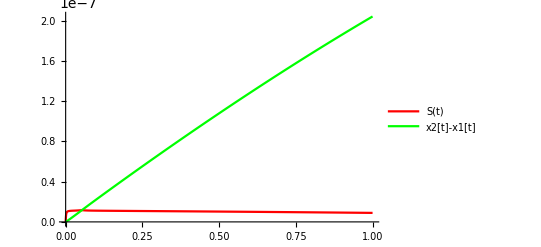

```mathematica
Show[Plot[Evaluate[x2'[t]*τ/.ntwoprime],{t,0,10^-13},PlotRange->All,PlotStyle->Red,PlotLegends->{"S(t)"}],Plot[Evaluate[x2[t]-x1[t]/.n],{t,0,10^-13},PlotRange->All,PlotStyle->Green,PlotLegends->{"x2[t]-x1[t]"}]]
```

#### x2[t] - x1[t] for Time Interval [0,10^-11]

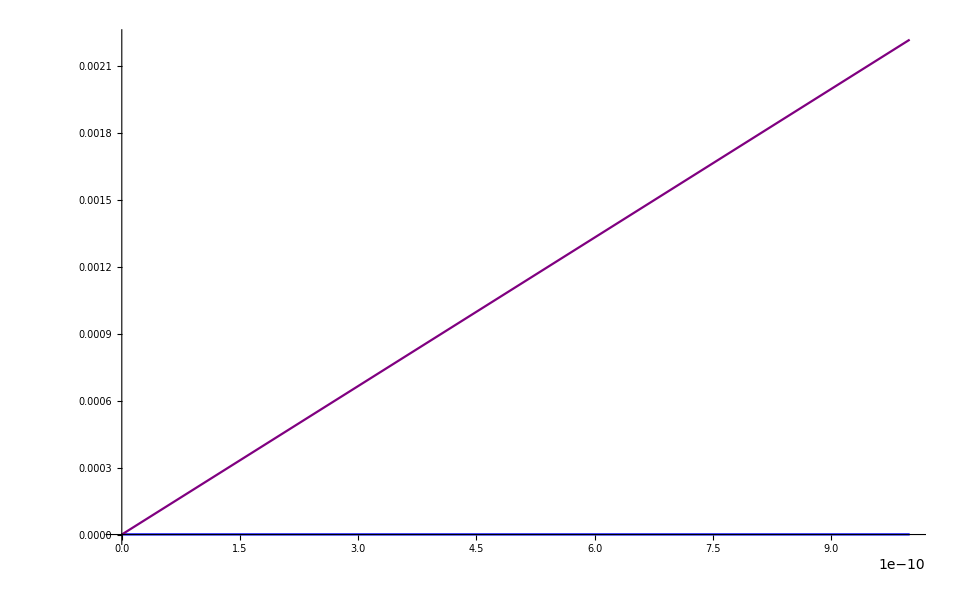

```mathematica
Show[Plot[Evaluate[x2[t]-x1[t]/.n],{t,0,10^-9},PlotRange->All,PlotStyle->Blue],Plot[Evaluate[x2[t]-x1[t]/.nos],{t,0,10^-9},PlotRange->All,PlotStyle->Purple,PlotLabel->{"PURPLE IS NO S"}]]
```

#### x2’[t]-x1’[t] for Time Interval [0,10^-9]

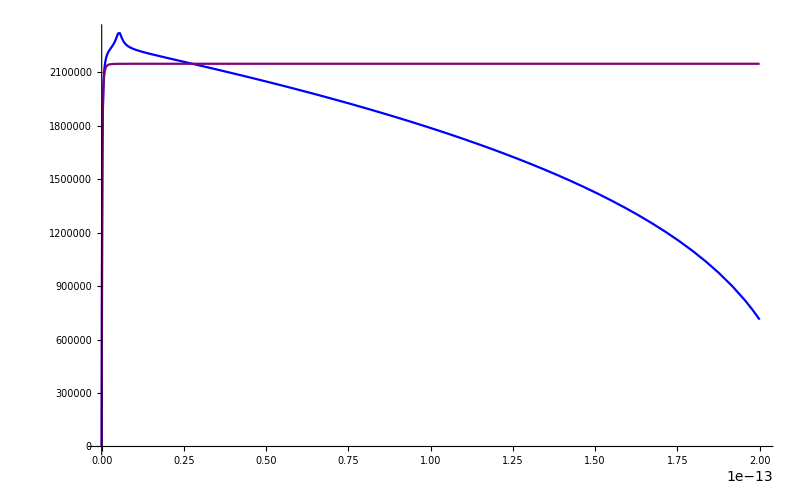

```mathematica
Show[Plot[Evaluate[x2'[t]-x1'[t]/.nprime],{t,0,2*10^-13},PlotStyle->Blue],Plot[Evaluate[x2'[t]-x1'[t]/.nosprime],{t,0,2*10^-13},PlotStyle->Purple,PlotRange->All]]
```

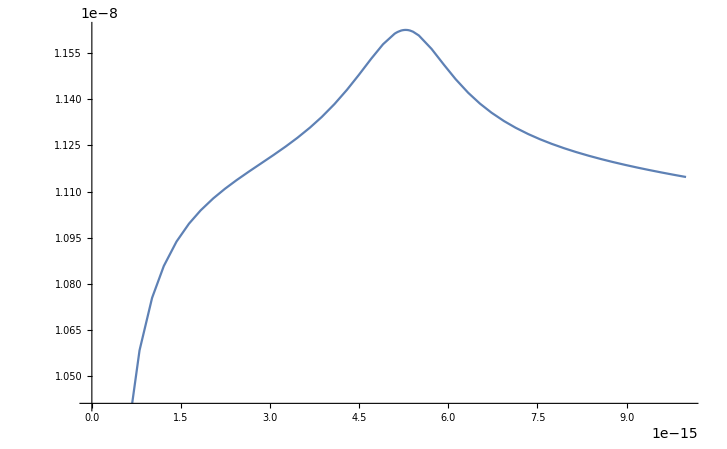

```mathematica
Plot[Evaluate[x2'[t]*10^-14/.ntwoprime],{t,0,10^-14}]
```

#### x2’[t]-x1’[t] for Time Interval [No S]

### Setting Values and Equations

```mathematica
Clear[k,xo,s1,s2,ϵo,q,d,τ,m,n,t,eq1,eq2]
Clear[Derivative]
q= 1.6021765×10^−19
τ=10^-14
m=9*10^-31
d=1 * 10^-9
ϵo=8.8541878128×10^−12

k=(1/ (4  π ϵo))
s1=τ x1'[t]
s2=τ x2'[t]
xo=(x2[t]-x1[t])

t3=10^-13

eq1=-(k*q^2 / m) * (1/xo^2) - (k *q^2 / m)* (s1/ (s1^2 + 4d^2)^(3/2)) + (k *q^2 / m)* ((xo-s2)/ ((xo-s2)^2 + 4d^2)^(3/2))

eq2 = (k*q^2 / m) * (1/xo^2) - (k *q^2 / m)* (s2/ (s2^2 + 4d^2)^(3/2)) - (k *q^2 / m)* ((xo+s1)/ ((xo+s1)^2 + 4d^2)^(3/2))




n=NDSolve[{x1''[t]-eq1==0,x2''[t]-eq2==0,x1[0]==-10^-10, x1'[0]==0,x2[0]==10^-10,x2'[0]==0},x2[t]-x1[t],{t,0,t3}]

ntwoprime=NDSolve[{x1''[t]-eq1==0,x2''[t]-eq2==0,x1[0]==-10^-10, x1'[0]==0,x2[0]==10^-10,x2'[0]==0},x2'[t],{t,0,t3}]

nprime=NDSolve[{x1''[t]-eq1==0,x2''[t]-eq2==0,x1[0]==-10^-10, x1'[0]==0,x2[0]==10^-10,x2'[0]==0}, x2'[t]-x1'[t],{t,0,t3}]
```

1.60218×10^-19

1/100000000000000

9/10000000000000000000000000000000

1/1000000000

8.85419×10^-12

8.98755×10^9

x1'[t]/100000000000000

x2'[t]/100000000000000

-x1[t]+x2[t]

1/10000000000000

-256.342/(-x1[t]+x2[t])^2-(2.56342×10^-12 x1'[t])/((1/250000000000000000+x1'[t]^2/10000000000000000000000000000)^(3/2))+(256.342 (-x1[t]+x2[t]-x2'[t]/100000000000000))/((1/250000000000000000+(-x1[t]+x2[t]-x2'[t]/100000000000000)^2)^(3/2))

256.342/(-x1[t]+x2[t])^2-(256.342 (-x1[t]+x2[t]+x1'[t]/100000000000000))/((1/250000000000000000+(-x1[t]+x2[t]+x1'[t]/100000000000000)^2)^(3/2))-(2.56342×10^-12 x2'[t])/((1/250000000000000000+x2'[t]^2/10000000000000000000000000000)^(3/2))

{{-x1[t]+x2[t]→-                                 -13
InterpolatingFunction[{{0., 1. 10   }}, <>][t]+                                 -13
InterpolatingFunction[{{0., 1. 10   }}, <>][t]}}

{{x2'[t]→                                 -13
InterpolatingFunction[{{0., 1. 10   }}, <>][t]}}

{{-x1'[t]+x2'[t]→-                                 -13
InterpolatingFunction[{{0., 1. 10   }}, <>][t]+                                 -13
InterpolatingFunction[{{0., 1. 10   }}, <>][t]}}

#### Setting a Second Set of Variables and Differential Equation to Manipulate

```mathematica
Clear[τ2,m2,t2,d2,s12,s22]
s12=0
s22=0


meq1=-(k*q^2 / m) * (1/xo^2) - (k *q^2 / m)* (s12/ (s12^2 + 4d^2)^(3/2)) + (k *q^2 / m)* ((xo-s22)/ ((xo-s22)^2 + 4d^2)^(3/2))

meq2 = (k*q^2 / m) * (1/xo^2) - (k *q^2 / m)* (s22/ (s22^2 + 4d^2)^(3/2)) - (k *q^2 / m)* ((xo+s12)/ ((xo+s12)^2 + 4d^2)^(3/2))



nos=NDSolve[{x1''[t]-meq1==0,x2''[t]-meq2==0,x1[0]==-10^-10, x1'[0]==0,x2[0]==10^-10,x2'[0]==0},x2[t]-x1[t],{t,0,t3}]

nosprime=NDSolve[{x1''[t]-meq1==0,x2''[t]-meq2==0,x1[0]==-10^-10, x1'[0]==0,x2[0]==10^-10,x2'[0]==0},x2'[t]-x1'[t],{t,0,t3}]
{{-x1[t]+x2[t]->-                                 -13
InterpolatingFunction[{{0., 1. 10   }}, <>][t]+                                 -13
InterpolatingFunction[{{0., 1. 10   }}, <>][t]}}
```

0

0

0.-256.342/(-x1[t]+x2[t])^2+(256.342 (-x1[t]+x2[t]))/((2.5×10^-19+(-x1[t]+x2[t])^2)^(3/2))

0.+256.342/(-x1[t]+x2[t])^2-(256.342 (-x1[t]+x2[t]))/((2.5×10^-19+(-x1[t]+x2[t])^2)^(3/2))

{{-x1[t]+x2[t]→-                                 -14
InterpolatingFunction[{{0., 2. 10   }}, <>][t]+                                 -14
InterpolatingFunction[{{0., 2. 10   }}, <>][t]}}

{{-x1'[t]+x2'[t]→-                                 -14
InterpolatingFunction[{{0., 2. 10   }}, <>][t]+                                 -14
InterpolatingFunction[{{0., 2. 10   }}, <>][t]}}

General::noinfo: Input expression                                  -13
InterpolatingFunction[{{0., 1. 10   }}, <>] contains insufficient information to interpret the result.

#### Outtake Manipulate Attempts

```mathematica
Manipulate[Plot[Evaluate[{x2[[τ2,m2,d2]][t2]-x1[[τ2,m2,d2]][t2]}/.msol],{t2,0,10^-14},PlotRange->All,PlotStyle->Purple,PlotLegends->{"τ[t2]","m[t2]","d[t2]"}],{τ2,0,10^-14},{m2,0,10^-27},{d2,0,10^-15}]


Plot[Evaluate[(x2[τ2,m2,d2][t2]-x1[[τ2,m2,d2]][t2]/.msol->1)/.sol],{t,0,10^-14},Filling->{2->{3}}]
```

```mathematica
Potential for Two Particles Moving Apart
```

```mathematica
U = 1 /b -1 / Sqrt[(b-a)^2+4] - 1 / Sqrt[(a^2+4)]
Manipulate[Plot[ {-A/(√(4+a^2))+A/b-A/(√(4+(-a+b)^2))},{b,10,1000},PlotStyle->Red],{a,0,0.1},{A,0,1}]
```

-1/(√(4+a^2))+1/b-1/(√(4+(-a+b)^2))

```mathematica
D[%666,b]
```

-1/b^2+(-a+b)/((4+(-a+b)^2)^(3/2))

```mathematica
D[%670,b]
```

2/b^3-(3 (-a+b)^2)/((4+(-a+b)^2)^(5/2))+1/((4+(-a+b)^2)^(3/2))

```mathematica
Solve[%685==0,b]
```

$Aborted

```mathematica
Clear[a,x]
FindMinimum[ {1 /x -1 / Sqrt[(x-0)^2+4] - 1 / Sqrt[(0^2+4)]},x]
```

{-0.5,{x→254452.}}

```mathematica
Manipulate[Plot[Evaluate[{x22[τ2,m2,d2][t2]-x12[τ2,m2,d2][t2]}/.msol],{t2,0,10^-14},PlotStyle->Purple,PlotRange->All,PlotLegends->{"τ","m","d"}],{τ2,0,10^-14},{m2,0,10^-27},{d2,0,10^-15}]


ReplaceAll::reps: "\!\(\*RowBox[{\"{\", \"msol\", \"}\"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing."
ReplaceAll::reps: "\!\(\*RowBox[{\"{\", \"msol\", \"}\"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing."
ReplaceAll::reps: "\!\(\*RowBox[{\"{\", \"msol\", \"}\"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing."
General::stop: "Further output of \!\(\*StyleBox[RowBox[{\"ReplaceAll\", \"::\", \"reps\"}], \"MessageName\"]\) will be suppressed during this calculation."
ReplaceAll::reps: "\!\(\*RowBox[{\"{\", \"msol\", \"}\"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing."
ReplaceAll::reps: "\!\(\*RowBox[{\"{\", \"msol\", \"}\"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing."
ReplaceAll::reps: "\!\(\*RowBox[{\"{\", \"msol\", \"}\"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing."
General::stop: "Further output of \!\(\*StyleBox[RowBox[{\"ReplaceAll\", \"::\", \"reps\"}], \"MessageName\"]\) will be suppressed during this calculation."
ReplaceAll::reps: "\!\(\*RowBox[{\"{\", \"msol\", \"}\"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing."
ReplaceAll::reps: "\!\(\*RowBox[{\"{\", \"msol\", \"}\"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing."
ReplaceAll::reps: "\!\(\*RowBox[{\"{\", \"msol\", \"}\"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing."
General::stop: "Further output of \!\(\*StyleBox[RowBox[{\"ReplaceAll\", \"::\", \"reps\"}], \"MessageName\"]\) will be suppressed during this calculation."
ReplaceAll::reps: "\!\(\*RowBox[{\"{\", \"msol\", \"}\"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing."
ReplaceAll::reps: "\!\(\*RowBox[{\"{\", \"msol\", \"}\"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing."
ReplaceAll::reps: "\!\(\*RowBox[{\"{\", \"msol\", \"}\"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing."
General::stop: "Further output of \!\(\*StyleBox[RowBox[{\"ReplaceAll\", \"::\", \"reps\"}], \"MessageName\"]\) will be suppressed during this calculation."
```

ReplaceAll::reps: {msol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.